# RF Modulation Sweep (Voltage)- Photon Correlation Counts

## Last Updated: 02/22/2022

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

```mathematica
(*todo: allow choice of which ind to sort by*)
```

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-03-28";
(*directoryString={
"Z://groups/motion/Data/2023-01-04",
"/Volumes/groups/motion/Data/2023-01-05"
};*)
```

```mathematica
(*select runs*)
ridList={15269};
```

```mathematica
(*number of histogram bins*)
histNumBins=100;
```

```mathematica
(*phase offset for fitting*)
phaseOffsetDJ=(-π*0.0)/2;
```

## Setup

## Plotting

```mathematica
(*set regular plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Sided Conversion

```mathematica
(*convert double-sided to single-sided*)
GetSingleSidedX[data_List]:=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]];
```

```mathematica
GetSingleSidedY[data_List]:=With[
{trimmedData=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]]},
Return[(2*#1-UnitVector[#2,1]*#1[[1]])&[trimmedData,Length[trimmedData]]]
];
```

## Import

## Import File

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString/@ridList]&];
```

## Extract Values

```mathematica
(*import hdf5 file and get labrad-style data*)
datafilesRaw=Import[#,{{"/datasets/voltage_array","/datasets/results"}}]&/@filenamesDJ;
```

```mathematica
(*get arguments*)
expIDStrings=Import[#,{"/expid"}]&/@filenamesDJ;
expIDStrings=ToExpression[StringReplace[#,":"->"->"]]&/@expIDStrings;
(*separate them into associations*)
expIDStringList=Association[#]&/@expIDStrings;
datasetArguments=#["arguments"]&/@expIDStringList;
```

```mathematica
(*get parameters*)
channelNames=Import[#,{"/datasets/channel_array"}]&/@filenamesDJ;
modulationAmplitudes=Import[#,{"/datasets/modulation_amplitude_vpp"}]&/@filenamesDJ;
modulationFrequencies=Import[#,{"/datasets/modulation_frequency_hz"}]&/@filenamesDJ;
```

## Process

## Formatting

### Combine Datasets Into Single

```mathematica
(*combine raw data into single list*)
datasets=AssociationThread[#[[1]]->#[[2]]]&/@datafilesRaw;
datasets=Merge[datasets,Join@@#&];
```

```mathematica
(*separate out x-array for future use*)
datasetKeys=Keys[datasets];
```

```mathematica
(*sort values by x-array*)
datasets=KeySort[datasets];
```

```mathematica
(*temporary - reduce to 1-dimension for now*)
channelNames=First@channelNames;
modulationAmplitudes=First@modulationAmplitudes;
modulationFrequencies=First@modulationFrequencies;
```

## Convert

```mathematica
(*todo: is this necessary?*)
datasetsModulo=KeyValueMap[Mod[#2,N[1/(modulationFrequencies*1*^6)]]&,datasets];
datasets=AssociationThread[Keys[datasets]->datasetsModulo];
```

## Calculate Values

```mathematica
(*get data range for easy processing*)
xRanges={Min[#],Max[#]}&/@Transpose[Keys[datasets]];
```

```mathematica
(*get total points, which may be different since we occasionally time out*)
numPoints=Length/@datasets;
```

```mathematica
(*get histogram data*)
histData=HistogramList[#,histNumBins]&/@datasets;
histData=Transpose[{#[[1,;;-2]],#[[2]]}]&/@histData//N;
```

## Demodulation

```mathematica
(*calculate correlated signal*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*modulationFrequencies*1*^6)*(#2)-ⅈ*phaseOffsetDJ]]/Length[#2]&,
datasets
];
{correlatedAmplitude,correlatedPhase}=Transpose[AbsArg[correlatedSignal]];
```

## Plot

## Histogram

```mathematica
(*plot*)
histPlots=KeyValueMap[
ListPlot[
#2,
PlotRange->Full,
FrameLabel->{ 
{Style["Counts (arb.)",{Black,Directive[15]}],None},
{Style["Time (s)",{Black,Directive[15]}],Style[channelNames[[1]]<>" = "<>ToString[#1[[1]]]<>" V, "<>channelNames[[2]]<>" = "<>ToString[#1[[2]]]<>" V",{Black,Directive[15]}]}
}
]&,
histData
];
```

## Complex Signal

### Format Data

```mathematica
(*associate demodulated data with dataset keys*)
correlatedAmplitudeSorted=Join[datasetKeys,Transpose[{correlatedAmplitude}],2];
correlatedPhaseSorted=Join[datasetKeys,Transpose[{correlatedPhase}],2];
```

```mathematica
(*group data by first voltage values*)
correlatedAmplitudeGrouped=Sort/@GroupBy[correlatedAmplitudeSorted,First,#[[;;,2;;]]&];
correlatedPhaseGrouped=Sort/@GroupBy[correlatedPhaseSorted,First,#[[;;,2;;]]&];
```

### Create Individual 2-D Plots

```mathematica
(*amplitude plots*)
amplitudePlots=ListLinePlot[
#,
DataRange->datasetKeys[[2]],
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style[channelNames[[2]]<>" Voltage(V)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
]&/@correlatedAmplitudeGrouped;
```

```mathematica
(*phase plots*)
phasePlots=ListLinePlot[
Transpose[{#[[;;,1]],(#[[;;,2]])/π}],
DataRange->datasetKeys[[2]],
PlotRange->Full,
FrameLabel->{ 
{Style["Phase (π rad.)",{Black,Directive[15]}],None},
{Style[channelNames[[2]]<>" Voltage(V)",{Black,Directive[15]}],Style["Correlated Signal Phase - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
]&/@correlatedPhaseGrouped;
```

### Create 3D Plots

```mathematica
(*density plot*)
amplitudeDensityPlot=ListDensityPlot[correlatedAmplitudeSorted,
PlotLegends->Automatic,
FrameLabel->{ 
{Style[channelNames[[2]]<>" Voltage (V)",{Black,Directive[15]}],None},
{Style[channelNames[[1]]<>" Voltage (V)",{Black,Directive[15]}],Style["Stray Field Compensation - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
];
```

```mathematica
(*3d plot*)
amplitude3DPlot=ListPlot3D[correlatedAmplitudeSorted,
ImageSize->Large,
AxesLabel->{channelNames[[1]],channelNames[[2]],"Signal Amplitude"}
];
```

## Summary

```mathematica
(*get min values*)
minParams=correlatedAmplitudeSorted[[OrderingBy[correlatedAmplitudeSorted,Last,3]]];
minParamsTable=TableForm[
Transpose[{minParams[[;;,1]],minParams[[;;,2]],minParams[[;;,3]]}],
TableHeadings->{None,{channelNames[[1]],channelNames[[2]],"Correlated Fraction"}},
TableAlignments->{Right,Right,Right}
];
```

```mathematica
(*print results*)
Print["Modulation Amplitude (V): "<>ToString[modulationAmplitudes]]
Print["Modulation Frequency (MHz): "<>ToString[modulationFrequencies]]
{minParamsTable,amplitudeDensityPlot,amplitude3DPlot}
```

Modulation Amplitude (V): 0.4

Modulation Frequency (MHz): 1.19

{H Shim | V Shim | Correlated Fraction
36. | 12. | 0.00224052
36. | 98. | 0.00330563
36. | 60. | 0.00343055,-Graphics-,-Graphics3D-}

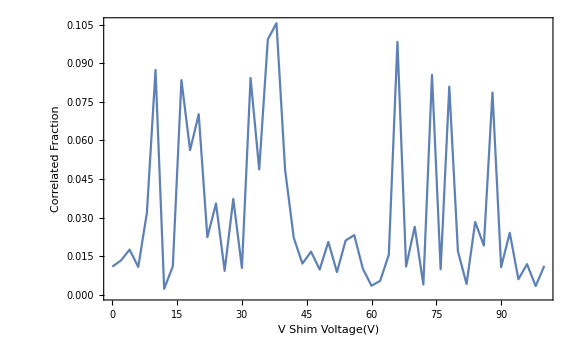
H Shim Voltage (V) | Correlated Amplitude Figure
36. | -Graphics-

```mathematica
(*print formatted amplitude plots for convenience*)
TableForm[
Transpose[{Keys[amplitudePlots],Values[amplitudePlots]}],
TableHeadings->{None,{channelNames[[1]]<>" Voltage (V)","Correlated Amplitude Figure"}},
TableAlignments->{Left,Right}
]
```

## Deprecated

## Importing

```mathematica
(*get parameters*)
(*xArr=Import[#,{"/datasets/xArr"}]*1*^6&/@filenamesDJ;
xArr=Sort/@xArr;*)
```

## Processing

```mathematica
(*get time difference in seconds*)
(*datasets=(#[[;;,3]]-#[[;;,2]])/(1*^9)&/@datafile;*)
```

```mathematica
(*get total count times*)
(*datasetTimes=N[(#[[-1,3]]-#[[1,2]])/(1*^9)]&/@datafile;*)
(*get total count rates*)
(*datasetRates=numPoints/datasetTimes;*)
```

## Fitting

### Preprocess

```mathematica
(*fitData=histData;*)
```

```mathematica
(*(*remove offset*)
(*fitData=#-Mean[#]&/@fitData[[;;,;;,2]];*)*)
```

```mathematica
(*(*fit constraints*)
fitConstraints={
0<=a<=40,
1*2*π<=b<=2*π*3,
0<=c<=2π
};*)
```

### Fitting

```mathematica
(*(*fit sine*)
AbsoluteTiming[dataFits=ParallelMap[
NonlinearModelFit[#,
Join[{a*Sin[b*x+c]+d},fitConstraints],
{a,b,c,d},x,
Method->Automatic,
MaxIterations->1000
]&,
histData
];]*)
```

```mathematica
(*(*extract parameters*)
fittedParameterTables=#["ParameterTable"][[1]]&/@dataFits;
fittedParameters=fittedParameterTables[[;;,1,2;;5,{2,3}]];
{fittedAmplitudes,fittedFrequencies,fittedPhases,fittedOffsets}=Transpose[fittedParameters];*)
```

### Plot Fit

```mathematica
(*fitSinFunc[A_,ω_,ϕ_,C_]:=A*Sin[ω*x+ϕ]+C;*)
```

```mathematica
(*(*create plot of fitted equation*)
fitSinEqns=fitSinFunc@@#&/@fittedParameters[[;;,;;,1]];
fitSinPlots=Plot[#,{x,histData[[1,1,1]],histData[[1,-1,1]]}]&/@fitSinEqns;*)
```

```mathematica
(*(*combine figures*)
combinedPlots=MapThread[Show[#1,#2]&,{histPlots,fitSinPlots}];*)
```

## Plotting

```mathematica
(*yz1=HistogramList[#,1000]&/@datasets;
mzdp1=Sqrt[GetSingleSidedY[Abs[Fourier[yz1[[1,2]]]]^2]];
ListLinePlot[%]*)
```

```mathematica
(*(*signal plots*)
{amplitudePlot,phasePlot}={
ListLinePlot[
correlatedAmplitude,
DataRange->xRange,
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Voltage (V)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
],
ListLinePlot[
correlatedPhase/π,
DataRange->xRange,
PlotRange->Full,
FrameLabel->{ 
{Style["Phase (π rad.)",{Black,Directive[15]}],None},
{Style["Voltage (V)",{Black,Directive[15]}],Style["Correlated Signal Phase - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
]
};*)
```

```mathematica
(*(*correlated rate minimization plot*)
correlatedRatePlot=ComplexListPlot[
Transpose[{correlatedSignal}],
(*PlotRange->Full,*)
PlotStyle->Table[
ColorData["Rainbow",i],
{i,0,1,1/(Length[correlatedSignal]-1)}
],
FrameLabel->{ 
{Style["⟨sin(ωt)⟩",{Black,Directive[15]}],None},
{Style["⟨cos(ωt)⟩",{Black,Directive[15]}],Style["Correlated Signal - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
},
PlotLegends->BarLegend["Rainbow"]
];*)
```

```mathematica
(*(*correlated rate minimization plot*)
correlatedRatePlot=ComplexListPlot[
Transpose[{correlatedSignal}],
(*PlotRange->Full,*)
PlotStyle->Table[
ColorData["Rainbow",i],
{i,0,1,1/(Length[correlatedSignal]-1)}
],
FrameLabel->{ 
{Style["⟨sin(ωt)⟩",{Black,Directive[15]}],None},
{Style["⟨cos(ωt)⟩",{Black,Directive[15]}],Style["Correlated Signal - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
},
PlotLegends->BarLegend["Rainbow"]
];*)
```

## Summary

```mathematica
(*Print["Modulation Amplitude (V): "<>ToString[modulationAmplitudes]]
Print["Modulation Frequency (MHz): "<>ToString[modulationFrequencies]]
{amplitudePlot,phasePlot}
(*correlatedRatePlot*)*)
```